```mathematica
(*Find root of an equation e starting from the point x=x0:
FindRoot[e, {x, x0}]*)
```

```mathematica
FindRoot[{x^3 + 2x^2 - x + 10 == 34, Log[y] + y^5 == 0}, {{x, 0}, {y, 1}}]
```

{x→2.44023,y→0.766941}

```mathematica
(*Insert number in equation*)
```

```mathematica
{x+y-1, x-10y-2}/.{x->1.0909090909090908,y->-0.09090909090909091}
```

{-8.32667×10^-17,0.}

```mathematica
(*Condition with complex body*)
```

```mathematica
a=0.2;
If[
a>=1, 
s := 2a; k := a^3, 
s := a-4; g := s^2/a
]
Print[s, ", ", k]
```

-3.8, 0.008

```mathematica
(*Union, intersection and complement of two sets A and B:
Union[A, B], Intersection[A, B], Complement[A, B]*)
```

```mathematica
A = {1, 2};
B = {2, 6};
Print[
Union[A, B],
Intersection[A, B],
Complement[A, B],
Complement[B, A]
]
```

{1,2,6}{2}{1}{6}

```mathematica
(*Limit of f(x) when x approaches a:
Limit[f(x), x -> a]*)
```

```mathematica
Limit[(x - 1)/(x+1), x-> Infinity]
```

1

```mathematica
Limit[Sin[x]/x, x->0]
```

1

```mathematica
(*Derivative of f(x) with respect to x:
D[f(x), x]*)
```

```mathematica
D[Cos[x], x]
```

-Sin[x]

```mathematica
(*Derivative of f(x) with respect to x for n times:
D[f(x), {x, n}]*)
```

```mathematica
D[Sin[x], {x, 3}]
```

-Cos[x]

```mathematica
(*Find maximum or minimum of a list of numbers l:
Max[l], Min[l]*)
```

```mathematica
Max[{-2, 3, 1, 0}]
```

3

```mathematica
Min[{4, -4, 1/4}]
```

-4

```mathematica
(*Find maximum or minimum of f(x) when x is between a and b:
FindMaximum[f(x), {x, a, b}], FindMinimum[f(x), {x, a, b}]*)
```

```mathematica
FindMinimum[Sin[x^2 - 1], {x, 0, 1}]
```

{-0.841471,{x→1.52633×10^-10}}

```mathematica
FindMaximum[Sin[x^2 - 1], {x , 0, 1}]
```

{1.,{x→1.60337}}

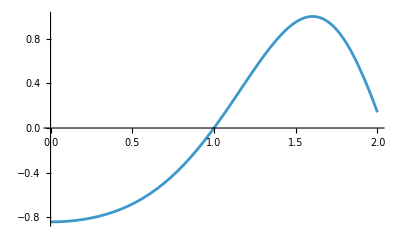

```mathematica
Plot[Sin[x^2 - 1], {x, 0, 2}]
```

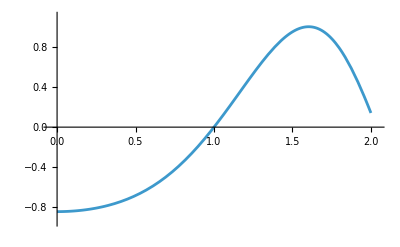

```mathematica
FindMaximum[Sin[x^2 - y], {{x, 0, 1}, {y, 0, 0.5}}]
```

{1.,{x→1.25331,y→-1.17311×10^-19}}

```mathematica
p1 = Plot3D[Sin[x^2 - y], {x, 0, 1.5}, {y, -1, 0.5}, PlotStyle->Pink];
p2 = Graphics3D[{Blue,PointSize[0.02],Point[{1.25331414126353,-1.1731075447227038*^-19,1.}]}];
Show[p1, p2]
```

-Graphics3D-

```mathematica
(*Indefinite integral of f(x):
Integrate[f(x), x]*)
```

```mathematica
Integrate[ArcCos[x]*x, x]
```

1/4 (-x √(1-x^2)+2 x^2 ArcCos[x]+ArcSin[x])

```mathematica
Integrate[E^(x^3), x]
```

-(x Gamma[1/3,-x^3])/(3 (-x^3)^(1/3))

```mathematica
(*Definite integral of f(x) when x is between a and b:
Integrate[f(x), {x, a, b}]*)
```

```mathematica
Integrate[ArcCos[x]*x, {x, 0, 1}]
```

π/8

```mathematica
(*Define series f(x) when x is close to a and number of sentences is b:
Series[f(x), {x, a, b}]*)
```

```mathematica
Series[1/(x^2 + 1), {x , 1, 12}]
```

1/2-(x-1)/2+1/4 (x-1)^2-1/8 (x-1)^4+1/8 (x-1)^5-1/16 (x-1)^6+1/32 (x-1)^8-1/32 (x-1)^9+1/64 (x-1)^10-1/128 (x-1)^12+O[x-1]^13

```mathematica
(*Get the series s without its remainder:
Normal[s]*)
```

```mathematica
Normal[Series[1/(x^2 + 1), {x , 1, 12}]]
```

1/2+(1-x)/2+1/4 (-1+x)^2-1/8 (-1+x)^4+1/8 (-1+x)^5-1/16 (-1+x)^6+1/32 (-1+x)^8-1/32 (-1+x)^9+1/64 (-1+x)^10-1/128 (-1+x)^12

```mathematica
(*Solve a differential equation*)
```

```mathematica
eq=D[y[x],{x,2}]+x D[y[x],x]-2-2x^2;
n=3;
yN[x_]=Sum[a[i] x^i,{i,0,n}];
eq1=yN[0] + 1;
eq2=yN[1]-0;
eq3[x_] = D[yN[x], {x, 2}] + x D[yN[x], x]- 2 - 2x^2;
A = CoefficientList[eq3[x], x];
B = Table[A[[i]], {i, 2, n}];
Flatten[AppendTo[B, {eq1, eq2}]];
yN[x]/.Solve[B == 0]
```

{-1+x^2}

```mathematica
eq=-D[y[x],{x,1}]+x D[y[x],x]-2+2 x^2==0;
sol=DSolve[eq,y[x],x]
```

{{y[x]→-2 (x+x^2/2)+C[1]}}